## Dynamic Analysis

-Graphics-

The purpose of dynamic analysis is to derive the equation of motion of the manipulator. In particular we want:
-Graphics-

### Direct Kinematics

```mathematica
Mrotxtrasl[α_, point_] := {{1,0,0, point[[1]]}, {0, Cos[α], -Sin[α], point[[2]]}, {0, Sin[α], Cos[α], point[[3]]}, {0, 0, 0, 1}} (*Roto trasl about x axis*)
Mrotxtrasl[α, {p1, p2, p3}] // MatrixForm
```

(1 | 0 | 0 | p1
0 | Cos[α] | -Sin[α] | p2
0 | Sin[α] | Cos[α] | p3
0 | 0 | 0 | 1)

```mathematica
EE = {0, L * Cos[θ[t]], L Sin[θ[t]], 1}; (*Point E with respect to RF0*)
M01 = Mrotxtrasl[θ[t], EE];
M01 // MatrixForm (*Now that we know the tranformation matrix of 01, we can compute the velocity matrix*)
W01 = Simplify[D[M01, t].Inverse[M01]];
W01 // MatrixForm

(*The same velocity matrix can be obtained by making use of the elicoidal tranformation matrix*)
Lrotx = {{0,0,0,0}, {0,0,-1, 0}, {0,1,0,0}, {0,0,0,0}};
Lrotx // MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[θ[t]] | -Sin[θ[t]] | L Cos[θ[t]]
0 | Sin[θ[t]] | Cos[θ[t]] | L Sin[θ[t]]
0 | 0 | 0 | 1)

(0 | 0 | 0 | 0
0 | 0 | -θ'[t] | 0
0 | θ'[t] | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L01 = Lrotx;
L01 * D[θ[t], t] // MatrixForm
W01.EE // MatrixForm (*Velocity of point EE in the RF0*)
```

(0 | 0 | 0 | 0
0 | 0 | -θ'[t] | 0
0 | θ'[t] | 0 | 0
0 | 0 | 0 | 0)

(0
-L Sin[θ[t]] θ'[t]
L Cos[θ[t]] θ'[t]
0)

### Lagrangian components

We are going to compute the Lagrangian components T (kinemat energy term) and U (potential energy term).

#### Kinematic energy

```mathematica
(*We have 2 masses, we'll need to compute 2 different kinematic contributions. For both of them we need the pseudo inertia tensor.
The tensor matrix is referred to a specific reference frame*)
```

-Graphics-

```mathematica
J11 = {{0,0,0,0}, {0, 1/3 *m1 * L^2, 0, -m1*L/2}, {0,0,0,0}, {0, -m1*L/2,0,m1}};
J11 // MatrixForm
```

(0 | 0 | 0 | 0
0 | (L^2 m1)/3 | 0 | -(L m1)/2
0 | 0 | 0 | 0
0 | -(L m1)/2 | 0 | m1)

```mathematica
(*Let's compute this transformation in order to express the tensor matrix in the absolute reference frame*)
J10 = M01.J11.Transpose[M01];
J10 // MatrixForm
```

(0 | 0 | 0 | 0
0 | 1/3 L^2 m1 Cos[θ[t]]^2 | 1/3 L^2 m1 Cos[θ[t]] Sin[θ[t]] | 1/2 L m1 Cos[θ[t]]
0 | 1/3 L^2 m1 Cos[θ[t]] Sin[θ[t]] | 1/3 L^2 m1 Sin[θ[t]]^2 | 1/2 L m1 Sin[θ[t]]
0 | 1/2 L m1 Cos[θ[t]] | 1/2 L m1 Sin[θ[t]] | m1)

```mathematica
(*Now i can compute the kinetic energy*)
T1 = Simplify[Tr[(1/2)*W01.J10.Transpose[W01]]]
```

1/6 L^2 m1 θ'[t]^2

```mathematica
(*Let's go with the second mass*)
J21 = {{0,0,0,0}, {0,0,0,0}, {0,0,0,0}, {0,0,0,m2}};
J21 // MatrixForm
J20 = M01.J21.Transpose[M01];
J20 // MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | m2)

(0 | 0 | 0 | 0
0 | L^2 m2 Cos[θ[t]]^2 | L^2 m2 Cos[θ[t]] Sin[θ[t]] | L m2 Cos[θ[t]]
0 | L^2 m2 Cos[θ[t]] Sin[θ[t]] | L^2 m2 Sin[θ[t]]^2 | L m2 Sin[θ[t]]
0 | L m2 Cos[θ[t]] | L m2 Sin[θ[t]] | m2)

```mathematica
W02 = W01;
T2 = Simplify[Tr[(1/2)*W02.J20.Transpose[W02]]]
```

1/2 L^2 m2 θ'[t]^2

#### Potential energy

-Graphics-

```mathematica
Hg1 = {{0,0,0,0}, {0,0,0,0}, {0,0,0, -g}, {0,0,0,0}} ;
Hg1 // MatrixForm
Ug1 = Tr[-Hg1.J10]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -g
0 | 0 | 0 | 0)

1/2 g L m1 Sin[θ[t]]

```mathematica
Hg2 = Hg1;
Ug2 = Tr[-Hg2.J20]
```

g L m2 Sin[θ[t]]

### Equation of motion

In order to compute the equation of motion, we are just missing the external actions. In this sense, we imagine to apply to our single link manipulator a torque given by a motor located in the origin of the absolute reference frame and a force applied along the arm.

-Graphics-

```mathematica
Q1 = C - 2F*L/3 (*External actions with respect RF0*)
Lagr = T1 + T2 - Ug1 - Ug2
```

C-(2 F L)/3

-1/2 g L m1 Sin[θ[t]]-g L m2 Sin[θ[t]]+1/6 L^2 m1 θ'[t]^2+1/2 L^2 m2 θ'[t]^2

```mathematica
dLdθ = D[Lagr, θ[t]]
```

-1/2 g L m1 Cos[θ[t]]-g L m2 Cos[θ[t]]

```mathematica
dLdθdot = D[Lagr, θ'[t]]
```

1/3 L^2 m1 θ'[t]+L^2 m2 θ'[t]

```mathematica
part1 = D[dLdθdot, t]
eq = part1 - dLdθ -Q1 == 0
```

1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]

-C+(2 F L)/3+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]==0

```mathematica
(*Imagine the external force F to be a viscous force*)
eqomtion = eq /. {F -> α * D[θ[t], t]}
```

-C+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]+2/3 L α θ'[t]+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]==0

## Matrix approach for non-lagrangian components

```mathematica
part1 = D[dLdθdot, t]
```

1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]

```mathematica
eq = part1 - dLdθ - Q1 == 0
```

-C+(2 F L)/3+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]==0

In order to compute the non-lagrangian components (or generalized external actions) Q1, we could be
more formal by using the so-called action matrix ϕ. This is needed to express the external forces wrt to
the independent variables of the system, especially when we have multiple independent variables. The
matrix is representing the external actions on a specific variable and they are expressed wrt a specific
reference frame. This can then be transformed in the absolute reference frame using the usual logic.
Let’s show that, using this approach, even including the forces FO introduced by the hinge in the origin,
we reach to the same Q1 we obtained earlier

-Graphics-

```mathematica
Cx = C + 1 / 3 * F * L - F01z * L
```

C+(F L)/3-F01z L

```mathematica
Phi11 = {{0, -Cz, Cy, F01x}, {Cz, 0, -Cx, F01y}, {-Cy, Cx, 0, F01z-F}, {-F01x, -F01y, F-F01z, 0}};
Phi11 // MatrixForm
```

(0 | -Cz | Cy | F01x
Cz | 0 | -C-(F L)/3+F01z L | F01y
-Cy | C+(F L)/3-F01z L | 0 | -F+F01z
-F01x | -F01y | F-F01z | 0)

```mathematica
Phi10 = Simplify[M01.Phi11.Transpose[M01]];
Phi10 // MatrixForm
```

(0 | (-Cz+F01x L) Cos[θ[t]]-Cy Sin[θ[t]] | Cy Cos[θ[t]]+(-Cz+F01x L) Sin[θ[t]] | F01x
(Cz-F01x L) Cos[θ[t]]+Cy Sin[θ[t]] | 0 | -C+(2 F L)/3 | F01y Cos[θ[t]]+(F-F01z) Sin[θ[t]]
-Cy Cos[θ[t]]+(Cz-F01x L) Sin[θ[t]] | C-(2 F L)/3 | 0 | (-F+F01z) Cos[θ[t]]+F01y Sin[θ[t]]
-F01x | -F01y Cos[θ[t]]+(-F+F01z) Sin[θ[t]] | (F-F01z) Cos[θ[t]]-F01y Sin[θ[t]] | 0)

```mathematica
PSP[Mat1_, Mat2_] := Mat1⟦3,2⟧*Mat2⟦3,2⟧+Mat1⟦1,3⟧*Mat2⟦1,3⟧+Mat1⟦2,1⟧*Mat2⟦2,1⟧+Mat1⟦1,4⟧*Mat2⟦1,4⟧+Mat1⟦2,4⟧*Mat2⟦2,4⟧+Mat1⟦3,4⟧*Mat2⟦3,4⟧;
P1 = Simplify[PSP[Phi10, W01]] (*Generalized external power*)
```

(C-(2 F L)/3) θ'[t]

```mathematica
Q1 = P1 / θ'[t]
```

C-(2 F L)/3

```mathematica
eqmotion = eq /. {F -> α * D[θ[t], t]}
```

-C+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]+2/3 L α θ'[t]+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]==0

### Response to a sinsuoidal input

Let’s try now to apply an input to our system and monitor how it behaves. In this case, there’s no
closed loop control on the manipulator so the system will respond freely to the excitation.
Let’s first of all visualize how the system is behaving without external input

{θ[t]→InterpolatingFunction[…][t]}

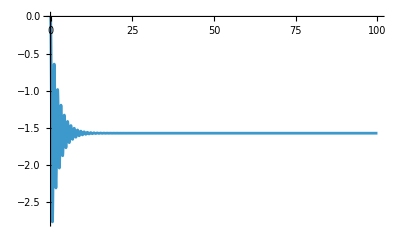

```mathematica
data = {L -> 0.3, m1 -> 15, m2 -> 8, α-> 5, g -> 9.81};
eqmotionnc = eqmotion /. C -> 0 /. data;
dsstaticnc=NDSolve[{eqmotionnc,θ[0]==0,θ'[0]==0},θ[t],{t,0,100}]⟦1⟧
Plot[θ[t] /. dsstaticnc, {t, 0, 100}, PlotRange->All]
```

```mathematica
motor={C->10*Sin[(2 π*0.1) t]} (*Function for the motor*)
e1=eqmotion/. motor/. data(*equation of motion with substituted data*)
```

{C→10 Sin[0.628319 t]}

45.6165 Cos[θ[t]]-10 Sin[0.628319 t]+1. θ'[t]+1.17 θ''[t]==0

```mathematica
ds1=NDSolve[{e1,θ[0]==0,θ'[0]==0},θ[t],{t,0,100}]
(*Numerically solving the equation of motion from t=0 s to t=100 s*
```

{{θ[t]→InterpolatingFunction[…][t]}}

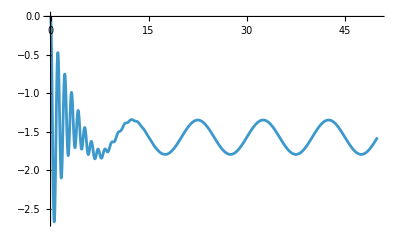

```mathematica
Plot[θ[t]/. ds1,{t,0,50},PlotRange->All] (*Plotting the whole solution*)
```

Notice that the arm starts near the vertical downward position (–π/2) because it is pulled down by
gravity. The transient towards the π/2 position (direction of gravitational force) is led by the viscous
and the inertial term resulting in the classical oscillations and, after that, it follows the sinusoidal
input. The arm is basically falling down and the moving periodically with the desired frequency.
The first step towards the goal of making the manipulator to track this input, is to avoid this phe-
nomenon. To do that we have to compensate gravity such that the arm is not falling down

### Gravity static compensation

## 20-11-2025

## Torque noise

```mathematica
gc = 45.6165 (*Last@Cstatic[[1]]*)
newC = (C /. C -> gc) + 0.001*Sin[2π*0.1t]
```

45.6165

45.6165+0.001 Sin[0.628319 t]

```mathematica
elbalanced = Expand[eqmotion /. C -> newC /. data]
```

-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]+1. θ'[t]+1.17 θ''[t]==0

```mathematica
dsbalanced = NDSolve[{elbalanced, θ[0] == 0, θ'[0] == 0}, θ[t], {t, 0, 100}][[1]]
```

{θ[t]→InterpolatingFunction[…][t]}

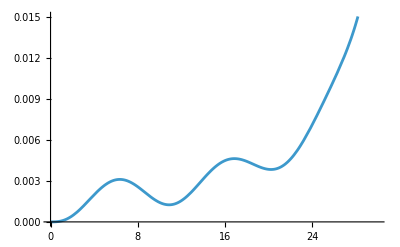

```mathematica
Plot[θ[t] /. dsbalanced, {t, 0, 30}] (*and we get a divergent system because there is no control on it: as soon as the system is excited with noise, it diverges*)
```

## Position Control

```mathematica
eqmotion  (*dynamics of the manipulator*)
```

-C+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]+2/3 L α θ'[t]+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]==0

```mathematica
Ccontrolled = kp  * (θd - θ[t]) /. θd -> 0 /. kp -> 100; (*the rule of thumb is that the proportianl (the faster controller response) is the bigger one. The integral one (the one that guarantess 0 error at steady state) is slightly smaller and the derivative is tipically smaller because it amplifies also the noise*)
elcontrolled = eqmotion /. data /. C -> (Ccontrolled + 0.001 Sin[2π*0.1t])
```

45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]+100 θ[t]+1. θ'[t]+1.17 θ''[t]==0

```mathematica
dscontrolled = NDSolve[{elcontrolled, θ[0]==0, θ'[0]==0}, θ[t], {t, 0, 100}][[1]]
```

{θ[t]→InterpolatingFunction[…][t]}

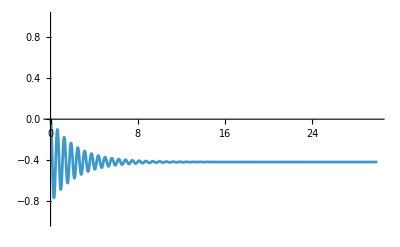

```mathematica
Plot[θ[t] /.dscontrolled, {t, 0, 30}, PlotRange->{-1, 1}]
```

```mathematica
Cplusgc = Ccontrolled + 0.001*Sin[2π * 0.1t] + gc (*controller plus gravity compensation. it will help to converge to 0*)
```

45.6165+0.001 Sin[0.628319 t]-100 θ[t]

-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]+100 θ[t]+1. θ'[t]+1.17 θ''[t]==0

{θ[t]→InterpolatingFunction[…][t]}

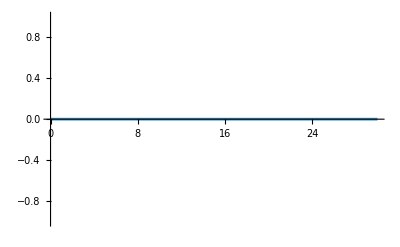

```mathematica
elcontrolledgc = eqmotion /. data /. C -> (Cplusgc)
dscontrolledgc = NDSolve[{elcontrolledgc, θ[0]==0, θ'[0]==0 }, θ[t], {t, 0, 100}][[1]]
Plot[θ[t] /. dscontrolledgc, {t, 0, 30}, PlotRange->{-1, 1}] (*In this way removed all the oscillations by removing the gravity bias compensation. there is gravity that pulls down the manipulator. The compensation makes the system much more easier to control*)
```

```mathematica
dscontrolledgc1 = NDSolve[{elcontrolledgc, θ[0] == 0, θ'[0] == 5}, θ[ŧ], {t, 0, 100}][[1]] (*Different starting velocity*)
Plot[θ[t] /. dscontrolledgc1, {t, 0, 30}, PlotRange->{-2, 2}]
```

{θ[ŧ]→InterpolatingFunction[…][ŧ]}

-Graphics-

```mathematica
dscontrolledgc2 = NDSolve[{elcontrolledgc, θ[0] == π/2, θ'[0] == 5}, θ[ŧ], {t, 0, 100}][[1]] (*Also different starting position*)
Plot[θ[t] /. dscontrolledgc2, {t, 0, 30}, PlotRange->{-2, 2}]
```

{θ[ŧ]→InterpolatingFunction[…][ŧ]}

-Graphics-

```mathematica
(*If you want to add some damping in the system you have to add a derivative term*)
(*actually there is a dmaping term of the system and we have to remove it (aerodynamic viscous force) in order to add a controlled one*)
(*Cause there is no damping, there's no way in which the system can dissipate energy*)
```

```mathematica
eqmotionnα = eqmotion /. α -> 0;
elcontrollednv = eqmotionnα /. C -> (Cplusgc) /. data
dscontrollednv = NDSolve[{elcontrollednv, θ[0] == π/2, θ'[0] == 0}, θ[t], {t, 0, 100}][[1]]
```

-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]+100 θ[t]+1.17 θ''[t]==0

{θ[t]→InterpolatingFunction[…][t]}

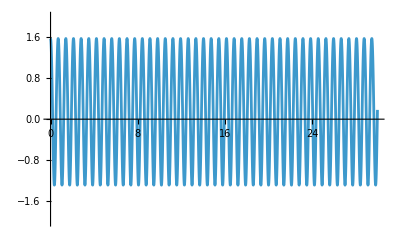

```mathematica
Plot[θ[t] /. dscontrollednv, {t, 0, 30}, PlotRange->{-2, 2}]
```

```mathematica
(*Now we can add dampign with our controller in order to reduce the oscillation of this result*)
Ccontrolled1 = kp(θd - θ[t]) - kd*θ'[t] /. θd -> 0 /. kp -> 100 /. kd -> 1
Cplusgc1 = Ccontrolled1 + 0.001 * Sin[2π * 0.1 t] + gc;
```

-100 θ[t]-θ'[t]

-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]+100 θ[t]+θ'[t]+1.17 θ''[t]==0

{θ[t]→InterpolatingFunction[…][t]}

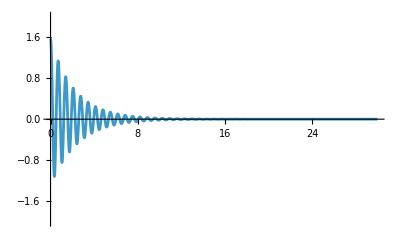

```mathematica
elcontrollednv1 = eqmotionnα /. C -> (Cplusgc1) /. data
dscontrollednv1 = NDSolve[{elcontrollednv1, θ[0] == π/2, θ'[0] == 0}, θ[t], {t, 0 , 100}][[1]]
Plot[θ[t] /. dscontrollednv1, {t, 0, 30}, PlotRange->{-2, 2}]
```

```mathematica
Ccontrolled2 = kp(θd - θ[t]) - kd * θ'[t] /. θd -> π/4 UnitStep[t - 1] /. kp -> 100 /. kd -> 10;
Cplusgc2 = Ccontrolled2 + 0.001Sin[2 π + 0.1t] + gc
```

45.6165+0.001 Sin[0.1 t]+100 (1/4 π UnitStep[-1+t]-θ[t])-10 θ'[t]

```mathematica
elcontrollednv2 = eqmotionnα /. C -> (Cplusgc2) /. data
dscontrollednv2 = NDSolve[{elcontrollednv2, θ[0] == π/2, θ'[0] == 0}, θ[t], {t, 0, 100}][[1]]
```

-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.1 t]-100 (1/4 π UnitStep[-1+t]-θ[t])+10 θ'[t]+1.17 θ''[t]==0

{θ[t]→InterpolatingFunction[…][t]}

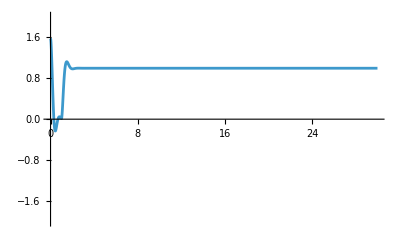

```mathematica
Plot[θ[t] /.dscontrollednv2, {t, 0, 30}, PlotRange->{-2, 2}] (*it's responding fast but it takes more than 1 second in order to reach the steady state and the band of the controller is not larger enough. In order to increase it we have to increase kp but not too much otherwise we have an aggressive controller*)
```

## Velocity + Position Control

```mathematica
(*NESTED CONTROL LOOP, IN WHICH THE INNER ONE, THAT IS VELOCITY, IS THE FASTER ONE*)
eqv = eqmotion /. α -> 0 /.C -> (kpv(ωd - D[θ[t], t]) + 0.001Sin[2π*0.1t]+gc)
eqp = eqv /.ωd -> kp(θd - θ[t]) // FullSimplify
elcontrolledpv = eqp /.data /.kp -> 100 /.kpv -> 50 /. θd -> π/4 UnitStep[t - 1]
```

-45.6165+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]-0.001 Sin[0.628319 t]-kpv (ωd-θ'[t])+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]==0

-45.6165-1. kp kpv θd+g L (0.5 m1+m2) Cos[θ[t]]-0.001 Sin[0.628319 t]+kp kpv θ[t]+kpv θ'[t]+L^2 (0.333333 m1+m2) θ''[t]==0

-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]-3926.99 UnitStep[-1+t]+5000 θ[t]+50 θ'[t]+1.17 θ''[t]==0

```mathematica
dscontrolledpv = NDSolve[{elcontrolledpv, θ[0] == π/2, θ'[0] == 0}, θ[t], {t,0,100}][[1]]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]-3926.99 UnitStep[-1+t]+5000 θ[t]+50 θ'[t]+1.17 θ''[t]==0,True,θ'[0]==0}.

{-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]-3926.99 UnitStep[-1+t]+5000 θ[t]+50 θ'[t]+1.17 θ''[t]==0,True,θ'[0]==0}

```mathematica
(*we can also remove the overshoots and oscillations in the discontinuity*)
```

```mathematica
eqp = eqv /. ωd -> kp(θd - θ[t]) - kd*θ'[t] // FullSimplify
elcontrolledpv1 = eqp /.data /.kp -> 100 /. kd -> 1 /. kpv -> 50 /. θd -> π/4 UnitStep[t - 1]
```

-45.6165-1. kp kpv θd+g L (0.5 m1+m2) Cos[θ[t]]-0.001 Sin[0.628319 t]+kp kpv θ[t]+(1+kd) kpv θ'[t]+L^2 (0.333333 m1+m2) θ''[t]==0

-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]-3926.99 UnitStep[-1+t]+5000 θ[t]+100 θ'[t]+1.17 θ''[t]==0

```mathematica
dscontrolledpv1 = NDSolve[{elcontrolledpv1,  θ[0] == π/2, θ'[0] == 5}, θ[t], {t, 0, 100}][[1]]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]-3926.99 UnitStep[-1+t]+5000 θ[t]+100 θ'[t]+1.17 θ''[t]==0,True,θ'[0]==5}.

{-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]-3926.99 UnitStep[-1+t]+5000 θ[t]+100 θ'[t]+1.17 θ''[t]==0,True,θ'[0]==5}

```mathematica
θsol[t_] := θ[t] /.dscontrolledpv1
θdotsol[t_]:=D[θsol[t], t]
θdes[t_]:= π/4 UnitStep[t - 1]
CM[t_]:=kpv(kp(θdes[t] - θsol[t]) -kd * (θdotsol[t] + 1))
CMsubs = CM[t] /. {kp -> 100, kd -> 1, kpv -> 50}
Plot[CMsubs, {t, 0, 30}, PlotRange->Full]
```

ReplaceAll::reps: {-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]-3926.99 UnitStep[-1+t]+5000 θ[t]+100 θ'[t]+1.17 θ''[t]==0,True,θ'[0]==5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

50 (-1-∂_t (θ[t]/.{-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]-3926.99 UnitStep[-1+t]+5000 θ[t]+100 θ'[t]+1.17 θ''[t]==0,True,θ'[0]==5})+100 (-(θ[t]/.{-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]-3926.99 UnitStep[-1+t]+5000 θ[t]+100 θ'[t]+1.17 θ''[t]==0,True,θ'[0]==5})+1/4 π UnitStep[-1+t]))

ReplaceAll::reps: {-45.6165+45.6165 Cos[θ[0.000612857]]+5000 θ[0.000612857]+100 θ'[0.000612857]+1.17 θ''[0.000612857]==0,True,θ'[0]==5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

D::ivar: 0.000612857 is not a valid variable.

ReplaceAll::reps: {-45.6165+45.6165 Cos[θ[0.000612857]]+5000 θ[0.000612857]+100 θ'[0.000612857]+1.17 θ''[0.000612857]==0,True,θ'[0]==5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-45.6165+45.6165 Cos[θ[0.000612857]]+5000. θ[0.000612857]+100. θ'[0.000612857]+1.17 θ''[0.000612857]==0.,True,θ'[0.]==5.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

D::ivar: 0.000612857 is not a valid variable.

D::ivar: 0.612858 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

-Graphics-

## Inverse Dynamics problem

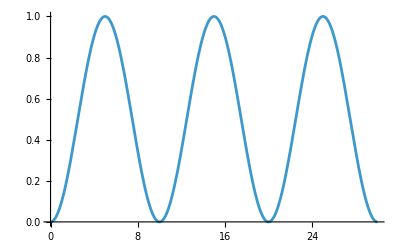

```mathematica
(*I want to impose a motion profile (i want that my angle moves in a specific way) and instead of having a controller we compute the inverse kinematics*)
MotionProfile[t_] := 1/2 (1 - Cos[2π * 0.1t]);
Plot[MotionProfile[t], {t, 0, 30}]
```

```mathematica
eqmotion
```

-C+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]+2/3 L α θ'[t]+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]==0

```mathematica
InverseDynamics = C/.Solve[eqmotion, C][[1]] // FullSimplify (*i put it on the other side*)
```

1/6 L (3 g (m1+2 m2) Cos[θ[t]]+4 α θ'[t]+2 L (m1+3 m2) θ''[t])

```mathematica
CommandTorque = InverseDynamics /.{θ[t] -> MotionProfile[t], θ'[t] -> D[MotionProfile[t], t], θ''[t] -> D[MotionProfile[t], t, t]}
```

1/6 L (0.394784 L (m1+3 m2) Cos[0.628319 t]+3 g (m1+2 m2) Cos[1/2 (1-Cos[0.628319 t])]+1.25664 α Sin[0.628319 t])

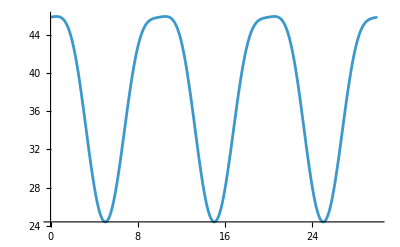

```mathematica
Plot[CommandTorque /. data, {t, 0, 30}]
```